# ICS Interaction Optimisation + Tuning Curves (Including Hourglass Effect)

SYMMETRIC i.e ROUND BEAMS ONLY!

## Units, Constants, Cases + Optimisation Parameters

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
```

```mathematica
CBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
headonCBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->0,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

headonDIANA687={Ee->687MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

MAXIIIeq={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinjheadon={Ee->700MeV,λ->1064nm,ϕ->0,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

HighMAXIIIinj={Ee->1520MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

CLS300NdYAG={Ee->99.71MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
CLS300HoYAG={Ee->99.71MeV,λ->2120nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
```

```mathematica
trialcase=headonDIANA687;
```

## Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
EL[λ_]:=(h*clight)/λ;
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_]:=(2+Xrec[Ee,λ])/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_]:=(1+ψ[Ee,θ]^2)/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*Δλ;
```

## Flux Intermediaries

```mathematica
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
zr[σL_,λ_]:=(4*π*σL^2)/λ;
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## β^* Calculation

```mathematica
βstar[Ee_,ϵn_,BW_,λ_,ΔEe_,Δλ_,θ_]:=(2*γ[Ee]*ϵn)/((1+Xrec[Ee,λ])*Sqrt[BW^2-(collterm[Ee,λ,θ]^2+beamspreadterm[Ee,λ,ΔEe,θ]^2+laserspreadterm[Ee,λ,Δλ,θ]^2)]);
```

## Angular Crossing + Hourglass Effect (Miyahara)

```mathematica
H[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_]:=Cos[ϕ/2]*Sqrt[(convxy[βIP,ϵn,Ee,σL]^2*convxy[βIP,ϵn,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
Uy[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIP_,Ee_,ϵn_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ/2]^2/(convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2)+Cos[ϕ/2]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_,λ_,Zc_]:=(H[ϕ,βIP,Ee,ϵn,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIP,Ee,ϵn,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Uy[βIP,Ee,ϵn,σL,λ]^2*Zc^2]);
```

## Uncollimated Flux Calculation

```mathematica
F[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_]:=σc[Ee,λ]*(Ne[Q]*NL[Epulse,λ]*f)/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Collimated Flux Calculation

```mathematica
Fψ[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,θ_,Zc_]:=Sqrt[2]/π*RACHG[ϕ,βIP,Ee,ϵn,σL,σze,tpulse,λ,Zc]*F[Ee,λ,Q,Epulse,f,ϕ,βIP,ϵn,σL]*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)*ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

# Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
BW=0.5/100;
θmax=5mrad;
θstep=10nrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

```mathematica
βstardat=Table[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
simtime={βstardat⟦1⟧};
```

```mathematica
imaginarycut=Min[Position[βstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[simtime,imaginarycut⟦1⟧];
```

```mathematica
βstardat=βstardat⟦2⟧⟦1;;(imaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[simtime,βstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Off[NIntegrate::izero]
```

```mathematica
Fψdat=Table[{βstardat⟦2⟧⟦i,1⟧,βstardat⟦2⟧⟦i,2⟧,NIntegrate[Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,βstardat⟦2⟧⟦i,1⟧,Zc]/.trialcase,{Zc,-0.1,0.1}]},{i,1,(imaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[simtime,Fψdat⟦1⟧];
```

```mathematica
maxval=Position[Fψdat⟦2⟧⟦All,3⟧,Max[Fψdat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

## Results

```mathematica
Grid[{{"Parameter","Symbol","Value","Unit"},{"Bandwidth","ΔE_γ/E_γ",BW*100,"%"},{"Collimation Angle","θ_col",(Fψdat⟦2⟧⟦maxval,1⟧)/mrad//N,"mrad"},{"β-function at the IP","β^*",Fψdat⟦2⟧⟦maxval,2⟧,"m"},{"Collimated Flux","F_ψ",Fψdat⟦2⟧⟦maxval,3⟧,"ph/s"},{"Simulation Time","t_sim",Total[simtime],"s"}},Dividers->{{True,True,True,True,True},{True,True,False,False,False,False,True}}]
```

Parameter | Symbol | Value | Unit
Bandwidth | ΔE_γ/E_γ | 0.5 | %
Collimation Angle | θ_col | 0.09181 | mrad
β-function at the IP | β^* | 0.603575 | m
Collimated Flux | F_ψ | 2.71107×10^9 | ph/s
Simulation Time | t_sim | 160.327 | s

# Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
BWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
BWmax=1/100;
BWstep=10^-3/100;
θmax=5mrad;
θstep=0.1μrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[βstar,BWmin,BWmax,BWstep,θmax,θstep,Fψ];
```

```mathematica
βstardatcurve=Table[{BW,ParallelTable[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]},{BW,BWmin,BWmax,BWstep}]//AbsoluteTiming;
```

```mathematica
simtime={βstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
imaginarycuts=Table[Min[Position[βstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,imaginarycuts⟦1⟧];
```

```mathematica
βstardatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦1;;(imaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,βstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[Fψ,βstardatcurve,imaginarycuts,BWmax,BWmin,BWstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::izero]];
```

```mathematica
Fψdatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,NIntegrate[Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,Zc]/.trialcase,{Zc,-0.1,0.1}]},{j,1,(imaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[simtime,Fψdatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
maxvals=Table[Position[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxvals⟦1⟧];
```

```mathematica
maxdata=Table[{Fψdatcurve⟦2⟧⟦i,1⟧*100,(Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,1⟧)/mrad,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,2⟧,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,3⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

```mathematica
Total[simtime]/60
```

69.3428

```mathematica
simtime
```

{2455.63,45.6563,16.7353,1641.12,0.84839,0.57773}

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/MAXIII NEQ-SR"];
maxdata⟦2⟧>>"MAXIIIinjheadonHGopt.txt";
```

## Plotting Data

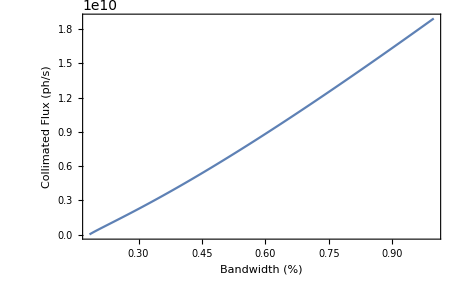

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,1⟧,maxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->16]
```

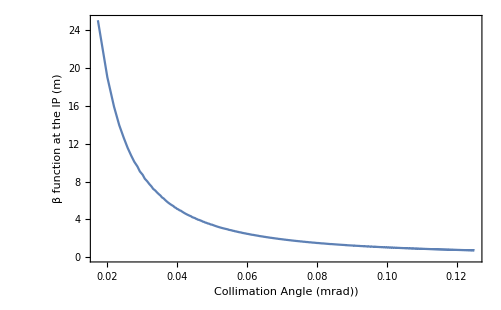

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,2⟧,maxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->16,PlotRange->All]
```

# Data Analysis

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat/MAXIII NEQ-SR"];
HGMAXIIIinjheadon=<<"MAXIIIinjheadonHGopt.txt";
NHGMAXIIIinjheadon=<<"MAXIIIinjheadonopt.txt";
```

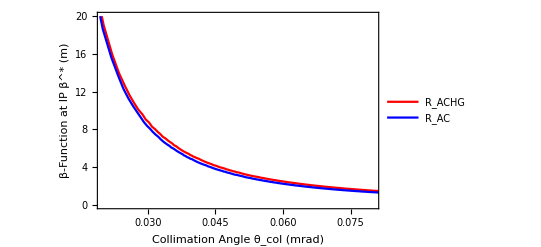

```mathematica
ListLinePlot[{Partition[Riffle[HGMAXIIIinjheadon⟦All,2⟧,HGMAXIIIinjheadon⟦All,3⟧],2],Partition[Riffle[NHGMAXIIIinjheadon⟦All,2⟧,NHGMAXIIIinjheadon⟦All,3⟧],2]},Frame->True,LabelStyle->15,FrameLabel->{"Collimation Angle θ_col (mrad)","β-Function at IP β^* (m)"},PlotStyle->{Red,Blue},PlotRange->{{0.02,0.08},{0,20}},PlotLegends->Placed[LineLegend[{"R_ACHG","R_AC"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

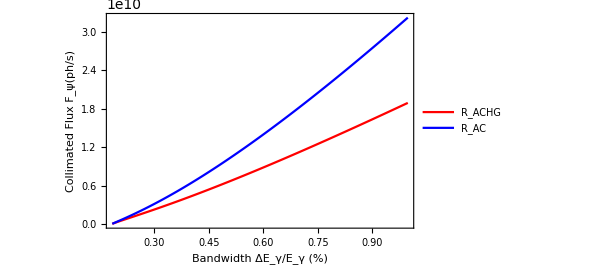

```mathematica
ListLinePlot[{Partition[Riffle[HGMAXIIIinjheadon⟦All,1⟧,HGMAXIIIinjheadon⟦All,4⟧],2],Partition[Riffle[NHGMAXIIIinjheadon⟦All,1⟧,NHGMAXIIIinjheadon⟦All,4⟧],2]},Frame->True,LabelStyle->15,FrameLabel->{"Bandwidth ΔE_γ/E_γ (%)","Collimated Flux F_ψ(ph/s)"},PlotStyle->{Red,Blue},PlotLegends->Placed[LineLegend[{"R_ACHG","R_AC"},LabelStyle->12,LegendFunction->frame],{0.3,0.7}]]
```